# Teeing Up Inequality: Tiger Woods and the Unintended Impact on Gender Prize Money

## By: Robbie Stirling and Joel Esparza

*Read at 75% Zoom in Wolfram Mathematica notebook for best view*

This project is broken up into four parts: Context, Time Analysis, Regression Analysis, and Textual Analysis. We will first introduce Tiger Woods and all the greatness that he experienced throughout his professional golfing career. His dominance in the sport led to great strides in the sport and business of professional golf. We will then analyze changes in different metrics throughout time. We will compare changes in PGA and LPGA when it comes to their annual income numbers. We will analyze and describe what is happening in these graphs as they will be the pieces of evidence that led us to perform a causal analysis. In our difference in differences analysis, we claim that the arrival of Tiger Woods to the PGA led to the wage gap between genders in professional golf to widened tremendously. Lastly, we will perform textual analysis on websites give better context on the aftermath by looking at present day disparities in professional golf.

## Background Knowledge

### Tiger Woods Timeline

There are very few athletes throughout human history that truly revolutionize their respective sports. Tiger Woods stands as a paradigm of this rare breed, a golfing prodigy who not only dominated the fairways but transformed the entire landscape of golf. Born Eldrick Tont Woods in 1975, Tiger’s journey into the world of golf began at an astonishingly young age. Introduced to the sport by his father, Earl Woods, himself an avid golfer and former Green Beret, Tiger exhibited an extraordinary talent that defied his years. Nicknamed ‘Tiger’ after a Vietnamese soldier Earl had befriended during the war, the young prodigy swiftly lived up to the moniker, showcasing an innate ability to master the intricacies of golf. His precocious talent became evident as he competed and won junior tournaments, and by the age of 2, he was already displaying an uncanny ability to mimic his father’s swing. As Tiger grew, so did the expectations surrounding him. He seamlessly transitioned from dominating the amateur circuit to rewriting records on the professional stage. His meteoric rise not only fulfilled the early promise but exceeded expectations, marking the emergence of a golfing phenomenon.

Winning tournament after tournament throughout the early stages of his career, his pure dominance during this reign can place him at the top of the list of one of the most dominant athletes to ever live. This puts him in the same tier of athletes such as Babe Ruth, Michael Jordan, Wayne Gretzky, and Mohammed Ali just to name a few. The timeline below helps us take a dive into Tiger’s illustrious golf career up to date. We see that from 1996-2003, this was peak Tiger Woods. This is where there was a clear golfer that was heads and shoulders above the rest. This is where he experienced majority of his winning. He has dealt with many problems that resulted in his decline, mostly due to injuries in his back and issues in his personal life. After little over a decade, Tiger Woods was able to win his last major championship in 2019 which puts him closer to the all time record.

## Creation of the Wage Gap in Professional Golf (Time Analysis)

## PGA Average Viewership of Major 4 Tournaments by Year

In this graph we can see how PGA’s average annual viewership of their top 4 tournaments changes throughout time. Before Tiger Woods enters the league, the average amount of viewers was ~20 million. Once he emerges into the league, we can see the average annual viewership increases at relatively high rates until it reaches ~30 million in 2002. It then stays relatively high for the next several years. In 2012, we can see viewership begin to decrease and continue to decrease until it reaches pre-Tiger Woods viewership numbers in 2021.

	Why is this important? The rise of Tiger Woods and his reign of pure dominance in the sport in his early years was able to attract large amounts of viewers to the point where he was able to increase the average viewership for each tournament by ~10 million. In the sports industry, viewership is what drives advances for both the sport and the business. This is no different for the sport and business of golf. This increase in viewership resulted in generating higher levels of revenue through more sponsorships, broadcasting rights, merchandise sales, and ticket sales. As a result of more money flowing into men’s golf, it is only appropriate if the people that are responsible for that viewership get a piece of it.

## Annual Salaries Throughout Time

We will now take a look at how the average annual winnings for PGA (men’s) players compares with that of LPGA (women’s) players. We can see that from 1987 to 1996, they move as close to parallel as it can get. However, once Tiger Woods enters the league, we can see the pink line for women’s increase at a relatively constant rate while the blue line for men’s increase exponentially. This parabolic shape that the average men’s winnings follows from 1996 -2002 indicates very high marginal increases. These rates were higher than other time period with the exception of post-Covid19. 

	This 6 year span from 1996-2002 was where the gap between average winnings for men’s became significantly larger than women’s. This dramatic increase throughout this time period resulted in a wage gap for genders in professional golf. Tiger Woods rise to stardom and the way he was able to captivate fans resulted in more money being generated to men’s golf, which then resulted in men earning higher money through winnings which further created this enormous wage gap that was not present in prior years.

## Annual Winning’s % Changes

This line graph shows us the percent changes of average annual winnings for both PGA and LPGA. For the most part, we can see that they tend to fluctuate simultaneous with each other. However, if we once again were to look between the time span of 1996-2002, it will tell a different story than the rest of the graph. These percentage increases throughout this time period can explain the parabolic shape that we saw in the previous graph. During this time span, we can see PGA reached levels of increases in their salaries by +5%, ~ +22%, +22%, +45%, +56%, +8%, and +19%. This year time span has 5 of the top 8 highest percent changes, including the two highest which are both more than double the third highest percent change in this graph (all with the exception of Covid).

## Cumulative Percent Changes of Average Annual Winnings

This graph shows us the cumulative percent changes of average annual winnings for both PGA and LPGA. We can see before the arrival of Tiger Woods, LPGA was yielding higher percent changes in average annual winnings compared to their male counterparts, PGA. However, once Tiger Woods enters the league, we once again see this parabolic shape between 1996-2002 . This resulted in a difference of 400% between genders in the year 2003. Until COVID-19 strikes, we can see that this 400% gap was relatively constant over the years. If it were not for these high percentage increases from 1996-2002, the wage gap between PGA and LPGA may still be similar to how it looked prior to the arrival of Woods ( refer to “Annual Salaries Throughout Time” from 1987-1996).

## Difference in Differences

After analyzing charts/graphs and conducting research into this topic, we wanted to apply our statistical analysis skills and explore more. Due to the fact that this entire project is claiming that Tiger Woods tremendously enlarged the wage gap between genders in professional golf, we felt that it would only be appropriate if we performed a causal analysis technique to truly understand his impact. The method we chose was a difference in difference curve where we created an interaction term to indicate the impact that the arrival of Tiger Woods has on PGA average winnings compared to average winnings to LPGA. 

We used the same dataset that was used for the line graphs in beginning of this project. We altered and manipulated our dataset a bit. We filtered for observations that were from 1988-2003. This way, we have the data for player winnings for both the 8 years before Woods arrived and the first 8 years of Wood’s career. In the dataset, rank, player, winnings, and year are pretty self explanatory. League is a binary variable that is 1 if the player is in the PGA and is 0 if the player is in the LPGA. Tiger is also a binary variable that is 1 if it is 1996 or after (Tiger’s arrival) and 0 if it is before. League_Tiger is an interaction term that is equal to League*Tiger. We will talk more about what these coefficients mean at the end our regression analysis.

```mathematica
SetDirectory[NotebookDirectory[]];
datare=Import["PGA_LPGA_SALARIES_2003.csv"];
Dimensions[datare];
Dataset[datare]
```

Dataset[<>]

```mathematica
headers=datare[[1,All]];
datareModified=Rest[datare[[All,1;;]]];
Dimensions[datareModified];
headersIndexed=Thread[Range[7]->headers[[1;;]]];
Grid[ArrayReshape[ResourceFunction["RecordsSummary"][datareModified],{3,4},""],Dividers->All,Alignment->{Left,Top}]
```

1 column 1
Min | 1
1st Qu | 65
Median | 129
Mean | 136.605
3rd Qu | 193
Max | 372 | 2 column 2
Allison Finney | 16
Andrew Magee | 16
Beth Daniel | 16
Betsy King | 16
Billy Andrade | 16
Billy Mayfair | 16
(Other) | 8120 | 3 column 3
Min | 153
1st Qu | 13612.5
Median | 70458.5
Mean | 224804.
3rd Qu | 235230.
Max | 9188321 | 4 column 4
Min | 1988
1st Qu | 1992
Median | 1995
Mean | 1995.37
3rd Qu | 1999
Max | 2003
5 column 5
1st Qu | 0
Min | 0
Mean | 0.610029
3rd Qu | 1
Max | 1
Median | 1 | 6 column 6
1st Qu | 0
Median | 0
Min | 0
Mean | 0.493549
3rd Qu | 1
Max | 1 | 7 column 7
1st Qu | 0
Median | 0
Min | 0
Mean | 0.294547
3rd Qu | 1
Max | 1 | 
 |  |  |

Winnings = 74,766.474  + 77,053.62* League + 69,930.84 * Tiger + 232,620.69 * League_Tiger

```mathematica
inputs3={{"74,766.474","This is the estimated average annual winnings for players in the LPGA (League = 0) when Tiger is before his arrival (Tiger = 0)"},{"77,053.62* League","If a player is in the PGA (League = 1) instead of the LPGA (League = 0), their average annual winnings are estimated to increase by $77,053.62, assuming Tiger is before his arrival"},{"69,930.84 * Tiger","If the year is after the arrival of Tiger Woods (Tiger = 1), the average annual winnings are estimated to increase by $69,930.84 for players in the LPGA (League = 0)"},{"232,620.69 * League_Tiger","The interaction term represents the additional impact on winnings when both in the PGA (League = 1) and after the arrival of Tiger Woods (Tiger = 1). Holding other variables constant, being in the PGA and after Tiger's arrival is associated with an additional increase of $232,620.69 in average annual winnings compared to the reference category (LPGA and before Tiger's arrival)"}};

(*Alternatively,using Grid*)
Grid[Prepend[inputs3,{"Coefficient","Meaning"}],Frame->All]
```

Coefficient | Meaning
74,766.474 | This is the estimated average annual winnings for players in the LPGA (League = 0) when Tiger is before his arrival (Tiger = 0)
77,053.62* League | If a player is in the PGA (League = 1) instead of the LPGA (League = 0), their average annual winnings are estimated to increase by $77,053.62, assuming Tiger is before his arrival
69,930.84 * Tiger | If the year is after the arrival of Tiger Woods (Tiger = 1), the average annual winnings are estimated to increase by $69,930.84 for players in the LPGA (League = 0)
232,620.69 * League_Tiger | The interaction term represents the additional impact on winnings when both in the PGA (League = 1) and after the arrival of Tiger Woods (Tiger = 1). Holding other variables constant, being in the PGA and after Tiger's arrival is associated with an additional increase of $232,620.69 in average annual winnings compared to the reference category (LPGA and before Tiger's arrival)

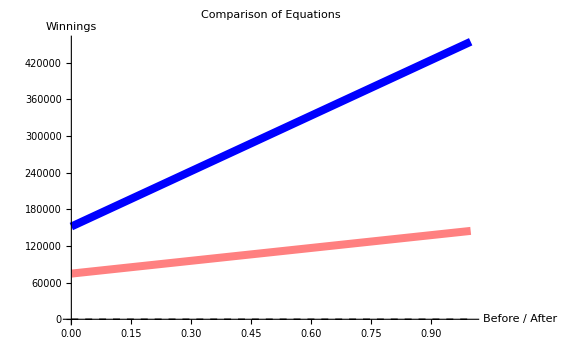

```mathematica
equation1[x_]:=74766.47+69930.84 x
equation2[x_]:=151820+302551.52 x

(*Generate data points for the lines*)
dataPoints1=Table[{x,equation1[x]},{x,{0,1}}];
dataPoints2=Table[{x,equation2[x]},{x,{0,1}}];

(*Plot the lines with a gap*)
ListLinePlot[{dataPoints1,dataPoints2},PlotStyle->{{Pink,Thickness[0.01]},{Blue,Thickness[0.01]}},AxesLabel->{"Before / After","Winnings"},PlotLabel->"Comparison of Equations",Epilog->{Dashed,Line[{{0,0},{1,0}}]},(*Dashed line for a gap*)ImageSize->Large]
```

The graph above can help us visualize the impact of Tiger Woods for the PGA. Before Tiger Woods (1988-1995), we see that there was a $77,053 gap between men average winnings and women’s average winnings. After the arrival of Tiger Woods in the PGA, we see that women’s witnessed a relatively small increase in average annual wages after the arrival of Tiger Woods by $69,930 For PGA however, they experienced an increase of $232,620.69 in average winnings. This shows the tremendous impact that Tiger Woods had on average golf winnings for the PGA and how it generated a wage gap that was unprecedented. Tiger Woods, a man who truly changed the game forever. These results give us statistically significant evidence supporting our claim that “Tiger Woods tremendously enlarged the wage gap between professional men and women golf players.

## Present Day Disparities in Professional Golf (Textual Analysis)

## PGA Website Homepage

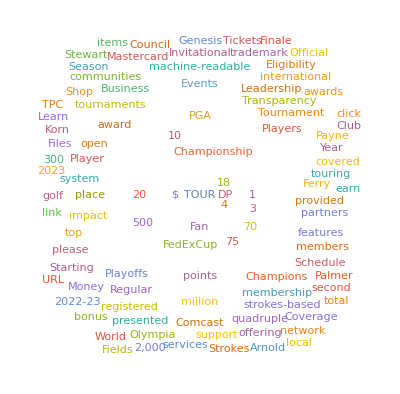

```mathematica
(*Uploading the About Us pages on the PGA website*)
urlPGA="https://www.pgatour.com/company/about";

(*Read the content from the URL as plaintext*)
webContentPGA=Import[urlPGA,"Plaintext"];

(*Remove common English words,if desired*)
filteredTextPGA=DeleteStopwords[webContentPGA];

(*Generate a word cloud with a limit on the number of words*)
WordCloud[filteredTextPGA,ImageSize->400]
```

```mathematica
(*Define lists of gender-specific words*)
maleWords={"he","his","him","male","man", "men"};
femaleWords={"she","her","female","woman", "girl", "women"};

(*Count occurrences of male and female words*)
maleWordCountPGAHome=Total[StringCount[webContentPGA,#,IgnoreCase->True]&/@maleWords];
femaleWordCountPGAHome=Total[StringCount[webContentPGA,#,IgnoreCase->True]&/@femaleWords];

(*Display the results*)
{maleWordCountPGAHome,femaleWordCountPGAHome};

TextGrid[{{"Number of male words", maleWordCountPGAHome}, {"Number of female words", femaleWordCountPGAHome}}, Frame->All]
```

Number of male words | 101
Number of female words | 7

## LPGA Website Homepage

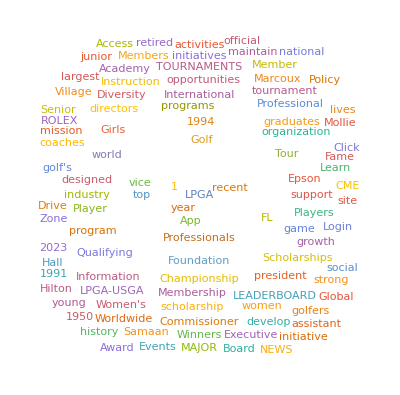

```mathematica
(*Repeating the steps for the LPGA About Us page now*)
urlLPGA="https://www.lpga.com/about-lpga";

(*Read the content from the URL as plaintext*)
webContentLPGA=Import[urlLPGA,"Plaintext"];

(*Remove common English words,if desired*)
filteredTextLPGA=DeleteStopwords[webContentLPGA];

(*Generate a word cloud with a limit on the number of words*)
WordCloud[filteredTextLPGA,ImageSize->400]
```

```mathematica
(*Define lists of gender-specific words*)
maleWords={"he","his","him","male","man", "men"};
femaleWords={"she","her","female","girl", "woman", "women"};

(*Count occurrences of male and female words*)
maleWordCountLPGAHome=Total[StringCount[webContentLPGA,#,IgnoreCase->True]&/@maleWords];
femaleWordCountLPGAHome=Total[StringCount[webContentLPGA,#,IgnoreCase->True]&/@femaleWords];

(*Display the results*)
{maleWordCountLPGAHome,femaleWordCountLPGAHome};

TextGrid[{{"Number of male words", maleWordCountLPGAHome}, {"Number of female words", femaleWordCountLPGAHome}}, Frame->All]
{225,57}
```

Number of male words | 225
Number of female words | 57

## LPGA Diversity Pages

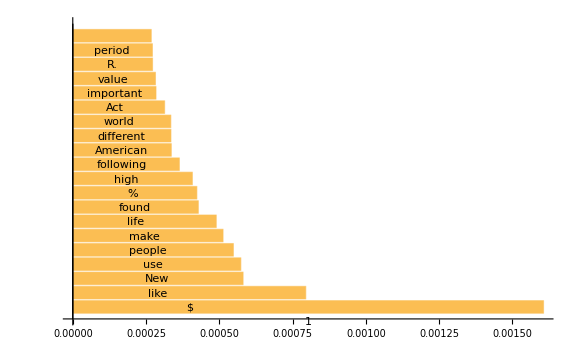

```mathematica
urlsDiversity={"https://www.lpga.com/diversity","https://www.lpga.com/diversity-policy","https://www.lpga.com/diverse-supplier-opportunity"};

getPageText[url_]:=StringJoin@Import[url,"Plaintext"]

textData=getPageText/@urlsDiversity;

(*Extract words from text and delete stopwords*)
wordsList=DeleteStopwords[TextWords[StringJoin[textData]]];

(*Limiting to Top 20 for visibility and readability*)
wordFrequencies=TakeLargest[WordFrequencyData[wordsList],20];

BarChart[wordFrequencies,ChartLabels->Placed[Keys[wordFrequencies],Below],BarOrigin->Left,ImageSize->Large]
```

## Textual Analysis Comparison

### Word Cloud

It is very interesting to see the different ways that each organization describes who they are and what they do. Analyzing the results from the PGA page there is quite a few mentions relating to money, the tournaments that they play throughout the year, and a lot of other words related to the business side of the operations. Comparing that to the LPGA page there aren’t any mentions of words related to money or earnings like there was with the PGA. They have more mentions of stuff related to how they are impacting their players and other things related to helping others whether it is the mentions of “assistance”, “opportunities”, or “Diversity”. They are in more of position where that is something they have to focus on to grow the game for women around the world. This backed up by the fact when I went to do an analysis of their Diversity pages, the PGA had no such tab on their website whereas the LPGA has a entire tab dedicated to the sub matter on the front page of their website. We thought it would interesting to analysis these pages on the LPGA website to see their areas of focus on improving diversity by looking at the frequency of words across the pages in the diversity tab.

### Diversity Pages (LPGA)

The word frequency analysis of diversity-related content across three different pages on the LPGA website reveals intriguing insights. After extracting and processing the text data from URLs focusing on diversity, the top 20 words were identified and visualized in a horizontal bar chart. Noteworthy terms include “$,” “New,” “%,” and “people,”. Not necessarily the most frequent words that you’d expect to find knowing the context of the text being analyzed. Without knowing the exact context in which these words are used, or symbols in the case of ‘%’ and ‘$’, it is difficult to fully understand the text being analyzed. There could be a lot of discussion between discrepancies in earnings among the sport, thus the ‘$’, or the ever changing demographics of the sport, thus the ‘%’. Those instances are why we thought it would be important to keep them included in the analysis. The LPGAs overall commitment to diversity on the girl’s tour and the sport of golf in general cannot be denied with the amount of content on their page being dedicated to the subject and the efforts they have made for change.

### Gender Specific Word Usage

The gender-specific word count analysis of the PGA and LPGA “About Us” pages reveals an interesting disparity in language usage. The PGA’s page leans heavily towards male-specific words, with a count of 101, while only mentioning female specific words only 7 times. On the other hand, the LPGA’s page also exhibits a higher count of male-specific words (225) however includes more female-specific mentions (57) compared to the PGA. This discrepancy could be attributed to a conscious effort by the LPGA to highlight inclusivity and emphasize the contributions of both genders within the sport. The LPGA, in its messaging, likely is drawing more parallels and comparisons with their male counterparts at the PGA, perhaps as a deliberate effort to highlight the disparities to highlight the shared excellence and achievements within the golfing world regardless of gender. Instead of being compared as separates, they see each other as equals not trying to create a divisible line between the two organizations. between the two tours or to highlight . It may reflect a strategic communication approach to challenge traditional gender norms and foster a more balanced representation within the golfing community. This could also indicate a response to the broader societal shift towards gender equality in sports, where the LPGA aims to celebrate and acknowledge the achievements of both male and female players.

## Sources

## Data

Sources :

PGA Tournament Earnings from the PGA Tour website

Download option per year

https://www.pgatour.com/stats/detail/109

LPGA Tournament Earnings from the LPGA Tour website

Web scrape the information from the website as there was no option to download

https://www.lpga.com/statistics/money/official-money?year=2023

PGA Viewership Numbers

https://www.sportsmediawatch.com/major-golf-ratings-historical-masters-us-open-british-pga-championship-tiger-woods/

Data Preparation

Remove unwanted columns

Remove NAs

Using R

Assign a year for data and add tour column to indicate PGA or LPGA

Combine all the data for each tour

Combine data into one concise table